# DFML_MathematicaInstructions

August H. Young (Frechette), Anil Ganti, Zbigniew J. Kabala

This interactive Mathematica Notebook contains the instructions required to properly utilize the flow solver in the package, ‘DFML_SolverModulePackage,’ and answer the questions posed in the laboratory instructions.

Edited: November 18 2022

## Reader’s Notes

Before proceeding further, it is important that you complete these steps:

Download the flow solver package, ‘DFML_SolverModulePackage’
Save this file to a folder of your choosing. Note the name and location of this folder as you will have to access it later.

When prompted to run initialization cells, select ‘Yes.’
Initialization cells are highlighted in gray.

If you are prompted to ‘enable dynamic formatting’ select ‘Enable.’

You may also wish to refer back to the following information:

Instructions have the following formatting:

Instructions.

Code you need to edit has the following formatting:

```mathematica
Edit me
```

Warning: 
DO NOT copy the contents of this notebook into your own notebook by cell. Certain cells have been marked as “un-editable.” This property will carry over if you copy these cells. You are encouraged to instead re-type the code to become more familiar with the Wolfram Language or copy the code text itself (to avoid syntax errors).

General trouble-shooting notes:

Cell evaluation: ‘shift’ (hold) + ‘return’

Variables that have been defined are black. Undefined variables are blue.

Clear the kernel: Evaluation >> Quit Kernel >> Local
This command is essentially like re-starting Mathematica. You will need to re-run all cells in your notebooks.

## Instructions: how to use the DFML_SolverModulePackage

## Initialization

This section walks you through the creation of a directory with the solver package, ‘DFML_SolverModulePackage.wl.’ This is the directory from which we will work.

First, we determine our current directory:

```mathematica
(*'shift' (hold) + 'return'*)
Directory[]
```

/Users/augustfrechette

Next, we set the directory of this notebook to be the same directory that the solver package is saved to. 
You will need to type this directory address into the ‘SetDirectory’ command.

In this case, the solver package is saved to the Desktop.

Note: Windows users will need to use backslashes rather than forward slashes, as illustrated here for Mac users.

```mathematica
(*'shift' (hold) + 'return'*)
SetDirectory["/Users/augustfrechette/Desktop"]
```

/Users/augustfrechette/Desktop

Load the solver file by executing the following cell:

```mathematica
(*'shift' (hold) + 'return'*)
<<DFML_SolverModulePackage.wl
```

Test that the solver file is properly loaded by inquiring about one of its functions, ‘GeoPlotter.’

```mathematica
(*'shift' (hold) + 'return'*)
?GeoModule
```

If you do not generate the description of ‘GeoModule’ provided above, you have not properly loaded the solver file.

## Parameter Generation

Determine what parameters to run through use of the GeoPlotter function.

```mathematica
GeoModule
```

Manually tweak these parameters until you’ve arrived at an acceptable Reynolds number and appropriate geometry (i.e., laminar flow conditions with W2> W1).

Copy your parameters for use in the flow solver into the variables below.

```mathematica
(*'shift' (hold) + 'return'*)
L = 0.04;
W1 = 0.01;
W2 = 0.02;
U = 0.04;
X1 = 0.01;
X2 = 0.03;
```

## Mesh Generation

Next, we need to pick a suitable mesh for this geometry.

```mathematica
(*'shift' (hold) + 'return'*)
?MeshModule
```

```mathematica
(*'shift' (hold) + 'return'*)
MeshModule
```

Manually tweak these parameters until you’ve arrived at a mesh you think will be acceptable for the flow solver.

Next, save the parameters that define our desired mesh in the format: mesh parameters (MP) = {max cell measure, max boundary cell measure}

```mathematica
MP ={0.000001,0.0005};
```

Note:
You may have to come back to this step if you did not pick suitable parameters. If we choose a mesh that is too coarse, or a Reynolds number in the transitional/turbulent flow regime, we will encounter error messages of the following type when we try to use our flow solver:

FindRoot::dfmin: The minimal damping factor of 1/10000 has been reached.

NDSolveValue::fempsf: PDESolve could not find a solution.

Come back to this section and refine your mesh or reduce your Reynolds number until these error messages go away.

## Data Generation

Input these parameters into the FlowModule.

```mathematica
(*'shift' (hold) + 'return'*)
?FlowModule
```

‘FlowModule’ has six outputs. If we input our saved parameters into this function, we will be given the following information:

The values: L, W1, W2, U, X1, X2, u[X1], U[X1], v[X1], p[X1], P[X1], u[X2], U[X2], v[X2], p[X2], P[X2]

A stream plot of the flow field

The interpolating function that represents the x-velocity field

The interpolating function that represents the y-velocity field

The interpolating function that represents the pressure field

The solver mesh

Using our saved parameters:

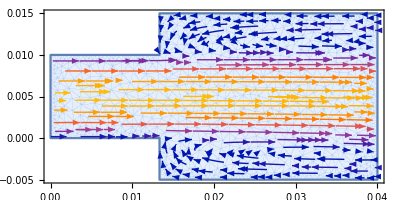
{{0.04,0.01,0.02,0.04,0.01,0.03,0.0599593,0.0399997,-0.0000897528,0.95269,0.951158,0.0580154,0.0199997,-0.000514117,0.970743,0.969995},-Graphics-,InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],ElementMesh[{{0.,0.04},{-0.005,0.015}},{TriangleElement[<1604>]}]}

```mathematica
(*'shift' (hold) + 'return'*)
results = FlowModule[L,W1,W2,U,X1,X2,MP]
```

To access any of these elements individually, use index notation.

```mathematica
(*'shift' (hold) + 'return'*)
results[[1]]
```

{0.04,0.01,0.02,0.04,0.01,0.03,0.0599593,0.0399997,-0.0000897528,0.95269,0.951158,0.0580154,0.0199997,-0.000514117,0.970743,0.969995}

To visualize the flow field, we can access the stream plot by probing the second item in the results variable:

```mathematica
(*'shift' (hold) + 'return'*)
results[[2]]
```

-Graphics-

To visualize the solver mesh, we can process the sixth item inn the results variable:

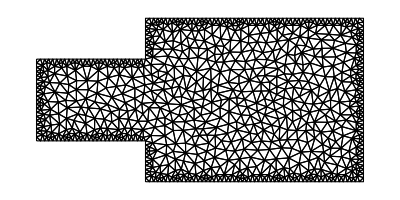

```mathematica
(*'shift' (hold) + 'return'*)
results[[6]]["Wireframe"]
```

## Data Collection

You will either need to complete manual data collection (similar to the outlined procedure above), or a parameter sweep.

Note: 
The parameter sweep is the faster method, however, if you are not careful, you may input a set of parameters that the flow solver cannot handle. Verify that your parameter sets are reasonable by first using the ‘GeoModule’ and ‘MeshModule’ functions!

### Manual Data Collection

In order to store our data, we will save it in a matrix, ‘Data’.

Initialize the ‘Data’ matrix.

```mathematica
(*'shift' (hold) + 'return'*)
Data={};
AppendTo[Data,{"L","W1","W2","U","X1","X2","u[X1]","U[X1]","v[X1]","p[X1]","P[X1]","u[X2]","U[X2]","v[X2]","p[X2]","P[X2]"}];
```

As is, our matrix is simply populated with column headers.

```mathematica
(*'shift' (hold) + 'return'*)
Data
```

{{L,W1,W2,U,X1,X2,u[X1],U[X1],v[X1],p[X1],P[X1],u[X2],U[X2],v[X2],p[X2],P[X2]}}

Save data to this matrix by running through a parameter set and assigning the results to ‘results.’

```mathematica
(*'shift' (hold) + 'return'*)
results = FlowModule[L,W1,W2,U,X1,X2,MP];
AppendTo[Data,results[[1]]];
Data // MatrixForm
```

(L | W1 | W2 | U | X1 | X2 | u[X1] | U[X1] | v[X1] | p[X1] | P[X1] | u[X2] | U[X2] | v[X2] | p[X2] | P[X2]
0.04 | 0.01 | 0.02 | 0.04 | 0.01 | 0.03 | 0.0599593 | 0.0399997 | -0.0000897528 | 0.95269 | 0.951158 | 0.0580154 | 0.0199997 | -0.000514117 | 0.970743 | 0.969995)

Change your parameters in the `Parameter Generation` section, and re-run the above cell to run the solver on your new parameters and append the results to the same ‘Data’ matrix. 

Note: Do not re-run the cell which initializes the ‘Data’ matrix unless you want to start all over!

In your laboratory instructions, you are asked to sweep through a range of Reynolds numbers or a range of aspect ratios (W1/W2). In this example, we adjust the flow domain and keep the inlet Reynolds number constant.

```mathematica
(*'shift' (hold) + 'return'*)
W2 = 0.03;
```

```mathematica
(*'shift' (hold) + 'return'*)
results = FlowModule[L,W1,W2,U,X1,X2,MP];
AppendTo[Data,results[[1]]];
Data // MatrixForm
```

(L | W1 | W2 | U | X1 | X2 | u[X1] | U[X1] | v[X1] | p[X1] | P[X1] | u[X2] | U[X2] | v[X2] | p[X2] | P[X2]
0.04 | 0.01 | 0.02 | 0.04 | 0.01 | 0.03 | 0.0599593 | 0.0399997 | -0.0000897528 | 0.95269 | 0.951158 | 0.0580154 | 0.0199997 | -0.000514117 | 0.970743 | 0.969995
0.04 | 0.01 | 0.03 | 0.04 | 0.01 | 0.03 | 0.059965 | 0.0400005 | 4.49883×10^-7 | 1.00012 | 0.998727 | 0.0583971 | 0.0133336 | 3.15525×10^-6 | 0.997854 | 0.997619)

Now you can begin to compare your results across different parameter sets as your new data is appended to the ‘Data’ matrix. 

Note: 
If you wish to save and compare stream plots, this is also something you can do. Go back to the beginning of this section wherein we accessed the solver mesh and streamplot.

When you’ve finished sweeping through aspect ratios (or Reynolds numbers), move on to the ‘Data Analysis’ Section.

### Parameter Sweep

Generate a set of parameters that either sweep over a range of Reynolds numbers or a range of aspect ratios (W1/W1).

In this example, we adjust the inlet Reynolds number by changing the average flow velocity, U.

```mathematica
(*'shift' (hold) + 'return'*)
Clear[L,W1,W2,U,X1,X2,Data,results]
L =0.06;
W1 = 0.02;
W2 = 0.025;
(*U = {} We will sweep through this parameter*)
Umin = 0.01; (*Minimum value of U we will sweep through*)
Umax = 0.05;(*Maximum value of U we will sweep through*)
dU = 0.01; (* U step size *)
X1 = 0.01;
X2 = 0.03;
```

Create a Table of all of your parameter inputs.

```mathematica
(*'shift' (hold) + 'return'*)
Trials = Table[{L,W1,W2,U,X1,X2,MP},{U,Umin,Umax,dU}];
Trials //MatrixForm
```

(0.06 | 0.02 | 0.025 | 0.01 | 0.01 | 0.03 | {1.×10^-6,0.0005}
0.06 | 0.02 | 0.025 | 0.02 | 0.01 | 0.03 | {1.×10^-6,0.0005}
0.06 | 0.02 | 0.025 | 0.03 | 0.01 | 0.03 | {1.×10^-6,0.0005}
0.06 | 0.02 | 0.025 | 0.04 | 0.01 | 0.03 | {1.×10^-6,0.0005}
0.06 | 0.02 | 0.025 | 0.05 | 0.01 | 0.03 | {1.×10^-6,0.0005})

Hint:
Here we use the `Table` command, which will loop through values of 'U', as specified by the second argument {U, Umin,Umax,dU}. Notice that 'U' shows up blue and not black. This indicates that it is the variable which Table will loop through.  Also notice that we did not define 'U' (it is commented out) when we defined our other parameters. You can edit the two cells above to sweep through a different parameter, like 'W2'.

Once you have a list of parameters you are happy with, we can pass it into the flow solver. This may take a while if your parameter sweep is long. The progress bar below will fill after each parameter set has been solved.

```mathematica
(*'shift' (hold) + 'return'*)
results = Monitor[Table[Apply[FlowModule,Trials[[i]]],{i,Length[Trials]}],ProgressIndicator[(i-1)/Length[Trials]]];
Data = Table[results[[i]][[1]],{i,Length[results]}];
PrependTo[Data,{"L","W1","W2","U","X1","X2","u[X1]","U[X1]","v[X1]","p[X1]","P[X1]","u[X2]","U[X2]","v[X2]","p[X2]","P[X2]"}];
Data //MatrixForm
```

(L | W1 | W2 | U | X1 | X2 | u[X1] | U[X1] | v[X1] | p[X1] | P[X1] | u[X2] | U[X2] | v[X2] | p[X2] | P[X2]
0.06 | 0.02 | 0.025 | 0.01 | 0.01 | 0.03 | 0.0149912 | 0.01 | 1.08718×10^-7 | 0.991704 | 0.991604 | 0.0143818 | 0.00799996 | -1.35251×10^-7 | 0.994726 | 0.99497
0.06 | 0.02 | 0.025 | 0.02 | 0.01 | 0.03 | 0.0299887 | 0.02 | 1.04825×10^-7 | 0.965875 | 0.965628 | 0.0292401 | 0.0159999 | -2.7318×10^-7 | 0.97612 | 0.976412
0.06 | 0.02 | 0.025 | 0.03 | 0.01 | 0.03 | 0.0449876 | 0.03 | 8.21651×10^-9 | 0.932114 | 0.931712 | 0.0441814 | 0.0239998 | -4.2038×10^-7 | 0.950125 | 0.95021
0.06 | 0.02 | 0.025 | 0.04 | 0.01 | 0.03 | 0.0599871 | 0.04 | -1.52881×10^-7 | 0.894171 | 0.893617 | 0.0591571 | 0.0319998 | -6.57122×10^-7 | 0.919677 | 0.91937
0.06 | 0.02 | 0.025 | 0.05 | 0.01 | 0.03 | 0.0749869 | 0.05 | -3.57868×10^-7 | 0.854047 | 0.853347 | 0.0741497 | 0.0399996 | -1.01119×10^-6 | 0.886528 | 0.885705)

Note: 
The following code still stores all outputs from the flow solver into the variable ‘results.’ Just the numerical values are stored in ‘Data.’

This is useful if we wanted to do something like visualize the change in the corner vortices accompanying an increase in the Reynolds number.

```mathematica
ListAnimate[Table[results[[i]][[2]],{i,Length[Trials]}]]
```

## Data Analysis

To complete the laboratory assignment, you can use the following hints provided in the Internal Processing section.

You will also want to export your data for safe-keeping.

### Export

Export your data by designating a file location and a filename.

In this example, we will use the same folder we made to save our flow solver to. 
We will call our export, ‘test_export,’ which will be saved as both CSV and XLSX files.

```mathematica
folder = "/Users/augustfrechette/Desktop/CEE301";
filename= "test_export.csv";
Export[FileNameJoin[{folder,filename}],Data,"CSV"];
filename= "test_export.xlsx";
Export[FileNameJoin[{folder,filename}],Data];
```

To verify that this export was successful, check your CEE301 folder for presence of these ‘test_export’ files.

### Internal Processing

Working in Mathematica allows for easy post-processing of our solver results.

For example, if we wanted analyze the pressure profile along the length of the channel, we could again probe the results variable to access the pressure field.
Remember, our ‘results’ variable is now a matrix, so accessing output elements looks a little different. For this example, let’s access the results that correspond to a mean channel velocity of U = 0.04.

```mathematica
ContourPlot[results[[4,5]][x,y],{x,y}∈results[[4,6]],PlotRange->Full,AspectRatio->Automatic, PlotLegends->Automatic]
```

-Graphics-

If we wanted to calculate the “true” loss coefficient for this parameter set, we could simply access the Data matrix.

K_L=  1-(v_2/v_1)^2+(p_1-p_2)/(1/2 ρ v_1^2)

```mathematica
ρ = 9.99*10^2;(*kg m^-3*)
u1 = Table[Data[[i,7]],{i,2,Length[Data],1}];
u2 =Table[Data[[i,12]],{i,2,Length[Data],1}];
p1=Table[Data[[i,10]],{i,2,Length[Data],1}];
p2=Table[Data[[i,15]],{i,2,Length[Data],1}];
klTrue = 1-(u2/u1)^2+(p1-p2)/(1/2 ρ u1^2)
```

-1.20891

Next, we can compare this value to the approximate loss coefficient.

K_L= ( 1-A_1/A_2)^2

```mathematica
A1 = Data[[4,2]];
A2 = Data[[4,3]]
klApprox = (1-A1/A2)^2;
```

0.04

If we wanted to plot our loss coefficients as a function of Reynolds number, we would use the ListPlot command.

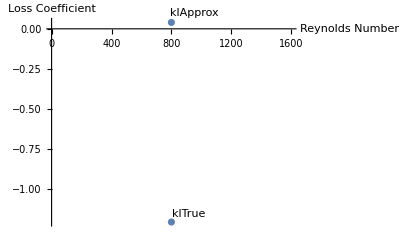

```mathematica
μ = 1.0005*10^-3;(*kg m^-1s^-1*)
U=Table[Data[[i,4]],{i,2,Length[Data],1}];
RE = W1*U*ρ/μ;
TrueData = Transpose[{RE,klTrue}];
ApproxData = Transpose[{RE,Table[klApprox,Length[RE]]}];
ListPlot[{Labeled[TrueData,"klTrue"],Labeled[ApproxData,"klApprox"]},AxesLabel->{"Reynolds Number","Loss Coefficient"}]
```

Looking to our laboratory assignment, we also see that we are asked to do things like plot the pressure variation across the channel width at X2. 
To serve as an example, we will plot the velocity profile of the flow at X1.

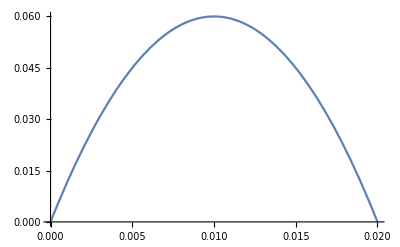

```mathematica
Plot[results[[4,3]][0.0001,y],{y,0,W2},PlotRange->All]
```

As expected, we obtain the Poiseuille velocity profile. If we wanted to verify that the magnitude of this profile is correct, we could, for instance, evaluate it’s average value.

```mathematica
NIntegrate[results[[4,3]][X1,y],{y,0,W1}]/W1
```

0.04

Let’s compare this to the U value we set:

```mathematica
U
```

0.04

We also see that the velocity profile abides by the no-slip condition we enforce in the flow solver:

```mathematica
Round[results[[4,3]][X1,W1]]
```

0

Our assignment also asks us to evaluate how the refinement of the solver mesh changes affects the quality of the solution you obtain. To conduct this analysis, you must change the mesh parameters, MP. Call on the meshPlotter module to visualize a coarser (or finer) mesh. Remember, a mesh that is too coarse, or too fine, will prevent solver convergence.

In this example, we will increase the interior and boundary cell size from our initial parameters MP = {0.000001, 0.0005}.

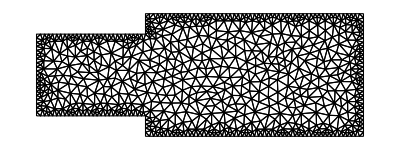

Let’s use mesh parameters MP = {0.000005,0.0006}

```mathematica
MeshModule
```

```mathematica
L = 0.04;
W1 = 0.01;
W2 = 0.015;
U = 0.04;
X1 = 0.01;
X2 = 0.03;
MPC ={0.000005,0.0006};
MPF ={0.000001,0.0005};

resultsC = FlowModule[L,W1,W2,U,X1,X2,MPC];
resultsF = FlowModule[L,W1,W2,U,X1,X2,MPF];
```

Let’s now compare the horizontal velocity profile at X2 for each mesh.

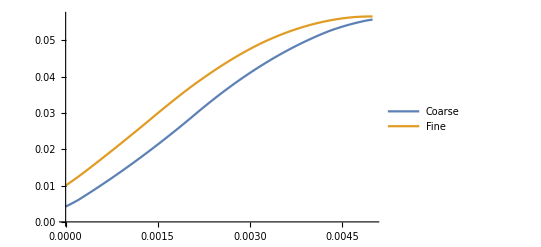

```mathematica
Plot[{resultsC[[3]][X2,y],resultsF[[3]][X2,y]},{y,0,W1/2},PlotLegends->{"Coarse","Fine"}]
```

Let’s look at the difference in our solutions to get an idea of the order of magnitude “error” we’re working with. Let’s also normalize this difference by the mean channel inlet velocity, U.

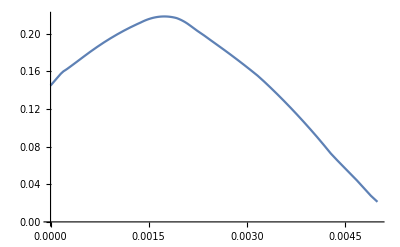

```mathematica
Plot[Abs[resultsF[[3]][X2,y]-resultsC[[3]][X2,y]]/U,{y,0,W1/2}]
```

Refinement in our solver mesh changes the value in our solution (in this cause the horizontal velocity profile) by 1% of the magnitude of the mean channel inlet velocity.